```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3+c04 x^4, 0≤x≤1}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3+c14(x-1)^4, 1<x≤2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3+c24(x-2)^4, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c01+c02+c03+c04

c11+c12+c13+c14

c21+c22+c23+c24

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+2]+f[x+1]+f[x]+f[x-1]+f[x-2]+f[x-3],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-2f[x+2]-f[x+1]+f[x-1]+2f[x-2]+3f[x-3],x>0&&x<1],x]
```

{2+c01+c02+c03+c04+c11+c12+c13+c14+c21+c22+c23+c24,-2 c02-3 c03-4 c04-2 c12-3 c13-4 c14-2 c22-3 c23-4 c24,2 c02+3 c03+4 c04+2 c12+3 c13+4 c14+2 c22+3 c23+4 c24+2 (c04+c14+c24),-4 (c04+c14+c24),2 (c04+c14+c24)}

{1+c01+c02+c03+c04+2 c11+2 c12+2 c13+2 c14+3 c21+3 c22+3 c23+3 c24,-c01-2 c02-3 c03-4 c04-3 c11-4 c12-6 c13-8 c14-5 c21-6 c22-9 c23-12 c24,c02+3 c03+6 c04+c12+6 c13+12 c14+c22+9 c23+18 c24,-c03-4 c04-3 c13-8 c14-5 c23-12 c24,c04+c14+c24}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	{c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c04→-1-c01-c02-c03,c14→-c11-c12-c13,c21→-9/5-(9 c01)/5-(4 c02)/5-(2 c03)/5-(7 c11)/5-(2 c12)/5-c13/5,c22→12/5+(12 c01)/5+(7 c02)/5+(6 c03)/5+(6 c11)/5+c12/5+(3 c13)/5,c23→-8/5-(8 c01)/5-(8 c02)/5-(9 c03)/5-(4 c11)/5-(4 c12)/5-(7 c13)/5,c24→1+c01+c02+c03+c11+c12+c13}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>3&&y<4]
}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1a6}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]],
	FullSimplify[D[SumF1a5,{{x,y}}]],
	FullSimplify[D[SumF1a6,{{x,y}}]]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-3&&y<-2]
}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5,DSumF1b6}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]],
	FullSimplify[D[SumF1b5,{{x,y}}]],
	FullSimplify[D[SumF1b6,{{x,y}}]]
}];
```

```mathematica
DSumF1a1=Simplify[DSumF1a1/.φ->1/2];
DSumF1a2=Simplify[DSumF1a2/.φ->1/2];
DSumF1a3=Simplify[DSumF1a3/.φ->1/2];
DSumF1a4=Simplify[DSumF1a4/.φ->1/2];
DSumF1a5=Simplify[DSumF1a5/.φ->1/2];
DSumF1a6=Simplify[DSumF1a6/.φ->1/2];
DSumF1b1=Simplify[DSumF1b1/.φ->1/2];
DSumF1b2=Simplify[DSumF1b2/.φ->1/2];
DSumF1b3=Simplify[DSumF1b3/.φ->1/2];
DSumF1b4=Simplify[DSumF1b4/.φ->1/2];
DSumF1b5=Simplify[DSumF1b5/.φ->1/2];
DSumF1b6=Simplify[DSumF1b6/.φ->1/2];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1a6}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-2^-1 (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_3^4 ∫_-2^-1 (DSumF1a6.{1,1})^2 ⅆxⅆy]
}];
{Err1b1,Err1b2,Err1b3,Err1b4,Err1b5,Err1b6}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_3^4 (DSumF1b5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-3^-2 ∫_3^4 (DSumF1b6.{1,1})^2 ⅆxⅆy]
}];
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1a6+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5+Err1b6];
```

```mathematica
Err=FullSimplify[Err1]
DErr=FullSimplify[D[Err,{{c01,c02,c03,c11,c12,c13}}]];
H=FullSimplify[D[Err,{{c01,c02,c03,c11,c12,c13},2}]];
NSols=NSolve[DErr==0,{c01,c02,c03,c11,c12,c13}];
TableForm[{Range[Length[NSols]],Err/.NSols,PositiveDefiniteMatrixQ[H/.N[#]]&/@NSols}ᵀ]
```

```mathematica
FindMinimum[Err,{{c01,-1},{c02,0},{c03,0},{c11,0},{c12,0},{c13,0}},Method->"Newton"]
FindMinimum[Err,{{c01,-1},{c02,0},{c03,0},{c11,0},{c12,0},{c13,0}},Method->"QuasiNewton"]
FindMinimum[Err,{{c01,-1},{c02,0},{c03,0},{c11,0},{c12,0},{c13,0}},Method->"ConjugateGradient"]
FindMinimum[Err,{{c01,-1},{c02,0},{c03,0},{c11,0},{c12,0},{c13,0}},Method->"PrincipalAxis"]
```

{0.029495,{c01→-0.443271,c02→-0.70886,c03→0.118277,c11→-0.54828,c12→0.389883,c13→0.141874}}

{0.029495,{c01→-0.443271,c02→-0.70886,c03→0.118277,c11→-0.54828,c12→0.389883,c13→0.141874}}

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.029495,{c01→-0.443261,c02→-0.708896,c03→0.118313,c11→-0.54829,c12→0.389918,c13→0.141836}}

{0.029495,{c01→-0.443272,c02→-0.708859,c03→0.118276,c11→-0.54828,c12→0.389882,c13→0.141875}}

```mathematica
FindMinimum[Err,{{c01,-0.43533022190806555967942052511996504447`10.226366502496674},{c02,-0.7533366962200895},{c03,0.18866691812815506},{c11,-0.54806244893545961068469588662520138975`9.012895622311857},{c12,0.37946785619540035693120056280664868902`8.451373514162633},{c13,0.16859459274005925375349532381855270073`7.954032520769908}},Method->"Newton"]
```

{0.029495,{c01→-0.443271,c02→-0.70886,c03→0.118277,c11→-0.54828,c12→0.389883,c13→0.141874}}

{c04→0.0338547,c14→0.0165229,c21→0.10093,c22→-0.00915814,c23→-0.0413939,c24→-0.0503776,c01→-0.443271,c02→-0.70886,c03→0.118277,c11→-0.54828,c12→0.389883,c13→0.141874}

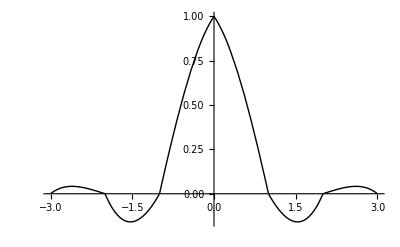

```mathematica
Sol={c01->-0.4432714716264854,c02->-0.708859891578325,c03->0.11827663982134162,c11->-0.548279764036396,c12->0.3898828766198676,c13->0.1418740156335347};
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```